```mathematica
data = Import[NotebookDirectory[]<>"../data/trainline/network.csv", "CSV"];
```

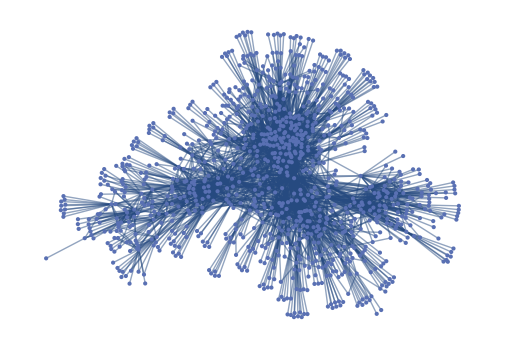

```mathematica
g = Graph[#1 <->#2 &@@@ data, VertexLabels->None, EdgeWeight->(#1 ->#2->#3 &@@@ data)];
GraphPlot[g]
```

```mathematica
data // Dataset
```

Dataset[<>]

```mathematica
geoLocationGraph = GeoPosition[{#5, #6}] <->GeoPosition[{#7, #8}]&@@@ data;
GeoGraphPlot[geoLocationGraph]
```

-Graphics-

```mathematica
GraphDistanceMatrix[geoLocationGraph] // ListPlot3D
```

```mathematica
DegreeGraphDistribution[geoLocationGraph]
```